```mathematica
HH=Table[A[i][j],{i,4},{j,4}]
```

{{A[1][1],A[1][2],A[1][3],A[1][4]},{A[2][1],A[2][2],A[2][3],A[2][4]},{A[3][1],A[3][2],A[3][3],A[3][4]},{A[4][1],A[4][2],A[4][3],A[4][4]}}

```mathematica
For[i=1,i≤4,i++,For[j=1,j≤4,j++,A[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

```mathematica
MatrixForm[HH]
```

((0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1))

### Define Σij=σi@σj

```mathematica
For[i=0,i≤3,i++,For[j=0,j≤3,j++,Σ[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

### Define Hamiltonian with parameters

```mathematica
m=2.5;
t0=1;
t0'=1;
t0''=1;
t=1;
t'=1;
t''=1;
ϕ=0.4;
```

```mathematica
Ham[kx_,ky_,kz_]:=(m-t0 Cos[kx]-t0' Cos[ky]-t0'' Cos[kz])Σ[0][3]+t Sin[(kx-ϕ)/2](Sin[kx/2] Σ[1][1]+Cos[kx/2] Σ[2][1])+t' Sin[ky] Σ[0][2]+t'' Sin[kz]Σ[3][1]
```

```mathematica
MatrixForm[Ham[kx,ky,kz]]
```

(2.5-Cos[kx]-Cos[ky]-Cos[kz] | -ⅈ Sin[ky]+Sin[kz] | 0 | Sin[1/2 (-0.4+kx)] (-ⅈ Cos[kx/2]+Sin[kx/2])
ⅈ Sin[ky]+Sin[kz] | -2.5+Cos[kx]+Cos[ky]+Cos[kz] | Sin[1/2 (-0.4+kx)] (-ⅈ Cos[kx/2]+Sin[kx/2]) | 0
0 | Sin[1/2 (-0.4+kx)] (ⅈ Cos[kx/2]+Sin[kx/2]) | 2.5-Cos[kx]-Cos[ky]-Cos[kz] | -ⅈ Sin[ky]-Sin[kz]
Sin[1/2 (-0.4+kx)] (ⅈ Cos[kx/2]+Sin[kx/2]) | 0 | ⅈ Sin[ky]-Sin[kz] | -2.5+Cos[kx]+Cos[ky]+Cos[kz])

### Define dispersion function and plot

```mathematica
F[kx_,ky_,kz_]:=Sort[N[Eigenvalues[Ham[kx+0.0,ky+0.0,kz+0.0]]]];
```

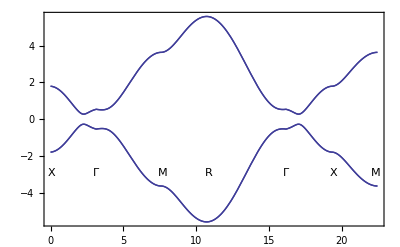

```mathematica
Plot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```

### Find the eigensystem and choose the two lower bands as VEC

```mathematica
ESYS[kx_,ky_,kz_]:=Eigensystem[Ham[kx,ky,kz]]
```

```mathematica
VEC[kx_,ky_,kz_]:=(Clear[VEC1,VEC2];For[i=1;j=1,i≤4,i++,If[ESYS[kx,ky,kz][[1]][[i]]<0,If[j==1,VEC1=ESYS[kx,ky,kz][[2]][[i]];j++,VEC2=ESYS[kx,ky,kz][[2]][[i]]]]];{VEC1,VEC2})
```

```mathematica
VEC[1,1,1]
```

{{-0.423849-0.129989 ⅈ,0.416941+0.785808 ⅈ,0.0606082-0.0919095 ⅈ,0.},{-0.0527819+0.0966166 ⅈ,0.,0.313484+0.313484 ⅈ,0.88957}}

### Build correlation function C[x,x’]

#### define numerical integral function

```mathematica
INT[y_,kx_,kz_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.1,int+=0.1y[kx,ii,kz,i,j]];int)
```

#### define the Core of Correlation function for integral

```mathematica
CORE[kx_,ky_,kz_,i_,j_]:=Exp[I (i-j) ky](KroneckerProduct[Conjugate[VEC[kx,ky,kz][[1]]],VEC[kx,ky,kz][[1]]]+KroneckerProduct[Conjugate[VEC[kx,ky,kz][[2]]],VEC[kx,ky,kz][[2]]])
```

#### define the Correlation function matrix, with 24 by 24

```mathematica
HCOR[kx_,kz_]:=(Clear[COR];Clear[OUT];OUT=Table[COR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,COR[iii][jjj]=INT[CORE ,kx,kz,-Pi,Pi,iii,jjj]]];OUT=ArrayFlatten[OUT])
```

```mathematica
MatrixForm[N[HCOR[1,1]]]
```

(0.926332+0. ⅈ | -1.56997-0.000135619 ⅈ | -4.19153×10^-17-3.1572×10^-17 ⅈ | -0.264338-0.483867 ⅈ | 0.395865-0.0000215619 ⅈ | -1.21611+0.000249785 ⅈ | -2.09167×10^-17-2.19733×10^-17 ⅈ | -0.0601858-0.110086 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.311362-0.000364127 ⅈ | 1.88696×10^-17-7.76129×10^-19 ⅈ | -0.0209003-0.038425 ⅈ | 0.00559039-0.0000647459 ⅈ | -0.104619+0.000478724 ⅈ | 1.16844×10^-17+6.707×10^-19 ⅈ | -0.0073211-0.0131502 ⅈ | 0.00172517+0.0000863983 ⅈ | -0.0433973-0.000593659 ⅈ | 3.26606×10^-17+9.88984×10^-18 ⅈ | -0.00332818-0.00642716 ⅈ | -0.000288429-0.000108111 ⅈ | -0.0133771+0.000709015 ⅈ | 8.88425×10^-18+2.12976×10^-17 ⅈ | -0.000933089-0.00128885 ⅈ
-1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.264338-0.483867 ⅈ | 0.+0. ⅈ | 0.501613-0.0000215469 ⅈ | -0.412672-0.000677887 ⅈ | -0.0601858-0.110086 ⅈ | 0.+0. ⅈ | 0.0622627-0.0000925095 ⅈ | -0.0192579+0.00135625 ⅈ | -0.0209003-0.038425 ⅈ | 0.+0. ⅈ | 0.0189099+0.00020663 ⅈ | -0.0223353-0.00203556 ⅈ | -0.0073211-0.0131502 ⅈ | 0.+0. ⅈ | 0.00218958-0.000320895 ⅈ | 0.0149653+0.00271631 ⅈ | -0.00332818-0.00642716 ⅈ | 0.+0. ⅈ | 0.00438825+0.000435385 ⅈ | -0.0163317-0.00339897 ⅈ | -0.000933089-0.00128885 ⅈ | 0.+0. ⅈ
-4.19153×10^-17+3.1572×10^-17 ⅈ | -0.264338+0.483867 ⅈ | 0.926332+0. ⅈ | 1.56997-0.000135619 ⅈ | -1.15565×10^-17-4.63953×10^-17 ⅈ | -0.0601155+0.110124 ⅈ | 0.395865-0.0000215619 ⅈ | -0.501613+0.0000215469 ⅈ | -2.02217×10^-17-2.40159×10^-17 ⅈ | -0.021041+0.0383481 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.0622627+0.0000925095 ⅈ | -1.05255×10^-18-1.63229×10^-17 ⅈ | -0.00710987+0.0132656 ⅈ | 0.00559039-0.0000647459 ⅈ | -0.0189099-0.00020663 ⅈ | 1.29326×10^-17-1.33498×10^-17 ⅈ | -0.00361004+0.00627317 ⅈ | 0.00172517+0.0000863983 ⅈ | -0.00218958+0.000320895 ⅈ | 2.11395×10^-17+1.55486×10^-17 ⅈ | -0.000580382+0.00148154 ⅈ | -0.000288429-0.000108111 ⅈ | -0.00438825-0.000435385 ⅈ
-0.264338+0.483867 ⅈ | 0.+0. ⅈ | 1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.0601155+0.110124 ⅈ | 0.+0. ⅈ | 1.21611-0.000249785 ⅈ | -0.412672-0.000677887 ⅈ | -0.021041+0.0383481 ⅈ | 0.+0. ⅈ | 0.311362+0.000364127 ⅈ | -0.0192579+0.00135625 ⅈ | -0.00710987+0.0132656 ⅈ | 0.+0. ⅈ | 0.104619-0.000478724 ⅈ | -0.0223353-0.00203556 ⅈ | -0.00361004+0.00627317 ⅈ | 0.+0. ⅈ | 0.0433973+0.000593659 ⅈ | 0.0149653+0.00271631 ⅈ | -0.000580382+0.00148154 ⅈ | 0.+0. ⅈ | 0.0133771-0.000709015 ⅈ | -0.0163317-0.00339897 ⅈ
0.395865+0.0000215619 ⅈ | 0.501613+0.0000215469 ⅈ | -1.15565×10^-17+4.63953×10^-17 ⅈ | -0.0601155-0.110124 ⅈ | 0.926332+0. ⅈ | -1.56997-0.000135619 ⅈ | -4.19153×10^-17-3.1572×10^-17 ⅈ | -0.264338-0.483867 ⅈ | 0.395865-0.0000215619 ⅈ | -1.21611+0.000249785 ⅈ | -2.09167×10^-17-2.19733×10^-17 ⅈ | -0.0601858-0.110086 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.311362-0.000364127 ⅈ | 1.88696×10^-17-7.76129×10^-19 ⅈ | -0.0209003-0.038425 ⅈ | 0.00559039-0.0000647459 ⅈ | -0.104619+0.000478724 ⅈ | 1.16844×10^-17+6.707×10^-19 ⅈ | -0.0073211-0.0131502 ⅈ | 0.00172517+0.0000863983 ⅈ | -0.0433973-0.000593659 ⅈ | 3.26606×10^-17+9.88984×10^-18 ⅈ | -0.00332818-0.00642716 ⅈ
-1.21611-0.000249785 ⅈ | -0.412672+0.000677887 ⅈ | -0.0601155-0.110124 ⅈ | 0.+0. ⅈ | -1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.264338-0.483867 ⅈ | 0.+0. ⅈ | 0.501613-0.0000215469 ⅈ | -0.412672-0.000677887 ⅈ | -0.0601858-0.110086 ⅈ | 0.+0. ⅈ | 0.0622627-0.0000925095 ⅈ | -0.0192579+0.00135625 ⅈ | -0.0209003-0.038425 ⅈ | 0.+0. ⅈ | 0.0189099+0.00020663 ⅈ | -0.0223353-0.00203556 ⅈ | -0.0073211-0.0131502 ⅈ | 0.+0. ⅈ | 0.00218958-0.000320895 ⅈ | 0.0149653+0.00271631 ⅈ | -0.00332818-0.00642716 ⅈ | 0.+0. ⅈ
-2.09167×10^-17+2.19733×10^-17 ⅈ | -0.0601858+0.110086 ⅈ | 0.395865+0.0000215619 ⅈ | 1.21611+0.000249785 ⅈ | -4.19153×10^-17+3.1572×10^-17 ⅈ | -0.264338+0.483867 ⅈ | 0.926332+0. ⅈ | 1.56997-0.000135619 ⅈ | -1.15565×10^-17-4.63953×10^-17 ⅈ | -0.0601155+0.110124 ⅈ | 0.395865-0.0000215619 ⅈ | -0.501613+0.0000215469 ⅈ | -2.02217×10^-17-2.40159×10^-17 ⅈ | -0.021041+0.0383481 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.0622627+0.0000925095 ⅈ | -1.05255×10^-18-1.63229×10^-17 ⅈ | -0.00710987+0.0132656 ⅈ | 0.00559039-0.0000647459 ⅈ | -0.0189099-0.00020663 ⅈ | 1.29326×10^-17-1.33498×10^-17 ⅈ | -0.00361004+0.00627317 ⅈ | 0.00172517+0.0000863983 ⅈ | -0.00218958+0.000320895 ⅈ
-0.0601858+0.110086 ⅈ | 0.+0. ⅈ | -0.501613-0.0000215469 ⅈ | -0.412672+0.000677887 ⅈ | -0.264338+0.483867 ⅈ | 0.+0. ⅈ | 1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.0601155+0.110124 ⅈ | 0.+0. ⅈ | 1.21611-0.000249785 ⅈ | -0.412672-0.000677887 ⅈ | -0.021041+0.0383481 ⅈ | 0.+0. ⅈ | 0.311362+0.000364127 ⅈ | -0.0192579+0.00135625 ⅈ | -0.00710987+0.0132656 ⅈ | 0.+0. ⅈ | 0.104619-0.000478724 ⅈ | -0.0223353-0.00203556 ⅈ | -0.00361004+0.00627317 ⅈ | 0.+0. ⅈ | 0.0433973+0.000593659 ⅈ | 0.0149653+0.00271631 ⅈ
0.0360416-0.0000431389 ⅈ | 0.0622627+0.0000925095 ⅈ | -2.02217×10^-17+2.40159×10^-17 ⅈ | -0.021041-0.0383481 ⅈ | 0.395865+0.0000215619 ⅈ | 0.501613+0.0000215469 ⅈ | -1.15565×10^-17+4.63953×10^-17 ⅈ | -0.0601155-0.110124 ⅈ | 0.926332+0. ⅈ | -1.56997-0.000135619 ⅈ | -4.19153×10^-17-3.1572×10^-17 ⅈ | -0.264338-0.483867 ⅈ | 0.395865-0.0000215619 ⅈ | -1.21611+0.000249785 ⅈ | -2.09167×10^-17-2.19733×10^-17 ⅈ | -0.0601858-0.110086 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.311362-0.000364127 ⅈ | 1.88696×10^-17-7.76129×10^-19 ⅈ | -0.0209003-0.038425 ⅈ | 0.00559039-0.0000647459 ⅈ | -0.104619+0.000478724 ⅈ | 1.16844×10^-17+6.707×10^-19 ⅈ | -0.0073211-0.0131502 ⅈ
-0.311362+0.000364127 ⅈ | -0.0192579-0.00135625 ⅈ | -0.021041-0.0383481 ⅈ | 0.+0. ⅈ | -1.21611-0.000249785 ⅈ | -0.412672+0.000677887 ⅈ | -0.0601155-0.110124 ⅈ | 0.+0. ⅈ | -1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.264338-0.483867 ⅈ | 0.+0. ⅈ | 0.501613-0.0000215469 ⅈ | -0.412672-0.000677887 ⅈ | -0.0601858-0.110086 ⅈ | 0.+0. ⅈ | 0.0622627-0.0000925095 ⅈ | -0.0192579+0.00135625 ⅈ | -0.0209003-0.038425 ⅈ | 0.+0. ⅈ | 0.0189099+0.00020663 ⅈ | -0.0223353-0.00203556 ⅈ | -0.0073211-0.0131502 ⅈ | 0.+0. ⅈ
1.88696×10^-17+7.76129×10^-19 ⅈ | -0.0209003+0.038425 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.311362-0.000364127 ⅈ | -2.09167×10^-17+2.19733×10^-17 ⅈ | -0.0601858+0.110086 ⅈ | 0.395865+0.0000215619 ⅈ | 1.21611+0.000249785 ⅈ | -4.19153×10^-17+3.1572×10^-17 ⅈ | -0.264338+0.483867 ⅈ | 0.926332+0. ⅈ | 1.56997-0.000135619 ⅈ | -1.15565×10^-17-4.63953×10^-17 ⅈ | -0.0601155+0.110124 ⅈ | 0.395865-0.0000215619 ⅈ | -0.501613+0.0000215469 ⅈ | -2.02217×10^-17-2.40159×10^-17 ⅈ | -0.021041+0.0383481 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.0622627+0.0000925095 ⅈ | -1.05255×10^-18-1.63229×10^-17 ⅈ | -0.00710987+0.0132656 ⅈ | 0.00559039-0.0000647459 ⅈ | -0.0189099-0.00020663 ⅈ
-0.0209003+0.038425 ⅈ | 0.+0. ⅈ | -0.0622627-0.0000925095 ⅈ | -0.0192579-0.00135625 ⅈ | -0.0601858+0.110086 ⅈ | 0.+0. ⅈ | -0.501613-0.0000215469 ⅈ | -0.412672+0.000677887 ⅈ | -0.264338+0.483867 ⅈ | 0.+0. ⅈ | 1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.0601155+0.110124 ⅈ | 0.+0. ⅈ | 1.21611-0.000249785 ⅈ | -0.412672-0.000677887 ⅈ | -0.021041+0.0383481 ⅈ | 0.+0. ⅈ | 0.311362+0.000364127 ⅈ | -0.0192579+0.00135625 ⅈ | -0.00710987+0.0132656 ⅈ | 0.+0. ⅈ | 0.104619-0.000478724 ⅈ | -0.0223353-0.00203556 ⅈ
0.00559039+0.0000647459 ⅈ | 0.0189099-0.00020663 ⅈ | -1.05255×10^-18+1.63229×10^-17 ⅈ | -0.00710987-0.0132656 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.0622627+0.0000925095 ⅈ | -2.02217×10^-17+2.40159×10^-17 ⅈ | -0.021041-0.0383481 ⅈ | 0.395865+0.0000215619 ⅈ | 0.501613+0.0000215469 ⅈ | -1.15565×10^-17+4.63953×10^-17 ⅈ | -0.0601155-0.110124 ⅈ | 0.926332+0. ⅈ | -1.56997-0.000135619 ⅈ | -4.19153×10^-17-3.1572×10^-17 ⅈ | -0.264338-0.483867 ⅈ | 0.395865-0.0000215619 ⅈ | -1.21611+0.000249785 ⅈ | -2.09167×10^-17-2.19733×10^-17 ⅈ | -0.0601858-0.110086 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.311362-0.000364127 ⅈ | 1.88696×10^-17-7.76129×10^-19 ⅈ | -0.0209003-0.038425 ⅈ
-0.104619-0.000478724 ⅈ | -0.0223353+0.00203556 ⅈ | -0.00710987-0.0132656 ⅈ | 0.+0. ⅈ | -0.311362+0.000364127 ⅈ | -0.0192579-0.00135625 ⅈ | -0.021041-0.0383481 ⅈ | 0.+0. ⅈ | -1.21611-0.000249785 ⅈ | -0.412672+0.000677887 ⅈ | -0.0601155-0.110124 ⅈ | 0.+0. ⅈ | -1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.264338-0.483867 ⅈ | 0.+0. ⅈ | 0.501613-0.0000215469 ⅈ | -0.412672-0.000677887 ⅈ | -0.0601858-0.110086 ⅈ | 0.+0. ⅈ | 0.0622627-0.0000925095 ⅈ | -0.0192579+0.00135625 ⅈ | -0.0209003-0.038425 ⅈ | 0.+0. ⅈ
1.16844×10^-17-6.707×10^-19 ⅈ | -0.0073211+0.0131502 ⅈ | 0.00559039+0.0000647459 ⅈ | 0.104619+0.000478724 ⅈ | 1.88696×10^-17+7.76129×10^-19 ⅈ | -0.0209003+0.038425 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.311362-0.000364127 ⅈ | -2.09167×10^-17+2.19733×10^-17 ⅈ | -0.0601858+0.110086 ⅈ | 0.395865+0.0000215619 ⅈ | 1.21611+0.000249785 ⅈ | -4.19153×10^-17+3.1572×10^-17 ⅈ | -0.264338+0.483867 ⅈ | 0.926332+0. ⅈ | 1.56997-0.000135619 ⅈ | -1.15565×10^-17-4.63953×10^-17 ⅈ | -0.0601155+0.110124 ⅈ | 0.395865-0.0000215619 ⅈ | -0.501613+0.0000215469 ⅈ | -2.02217×10^-17-2.40159×10^-17 ⅈ | -0.021041+0.0383481 ⅈ | 0.0360416+0.0000431389 ⅈ | -0.0622627+0.0000925095 ⅈ
-0.0073211+0.0131502 ⅈ | 0.+0. ⅈ | -0.0189099+0.00020663 ⅈ | -0.0223353+0.00203556 ⅈ | -0.0209003+0.038425 ⅈ | 0.+0. ⅈ | -0.0622627-0.0000925095 ⅈ | -0.0192579-0.00135625 ⅈ | -0.0601858+0.110086 ⅈ | 0.+0. ⅈ | -0.501613-0.0000215469 ⅈ | -0.412672+0.000677887 ⅈ | -0.264338+0.483867 ⅈ | 0.+0. ⅈ | 1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.0601155+0.110124 ⅈ | 0.+0. ⅈ | 1.21611-0.000249785 ⅈ | -0.412672-0.000677887 ⅈ | -0.021041+0.0383481 ⅈ | 0.+0. ⅈ | 0.311362+0.000364127 ⅈ | -0.0192579+0.00135625 ⅈ
0.00172517-0.0000863983 ⅈ | 0.00218958+0.000320895 ⅈ | 1.29326×10^-17+1.33498×10^-17 ⅈ | -0.00361004-0.00627317 ⅈ | 0.00559039+0.0000647459 ⅈ | 0.0189099-0.00020663 ⅈ | -1.05255×10^-18+1.63229×10^-17 ⅈ | -0.00710987-0.0132656 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.0622627+0.0000925095 ⅈ | -2.02217×10^-17+2.40159×10^-17 ⅈ | -0.021041-0.0383481 ⅈ | 0.395865+0.0000215619 ⅈ | 0.501613+0.0000215469 ⅈ | -1.15565×10^-17+4.63953×10^-17 ⅈ | -0.0601155-0.110124 ⅈ | 0.926332+0. ⅈ | -1.56997-0.000135619 ⅈ | -4.19153×10^-17-3.1572×10^-17 ⅈ | -0.264338-0.483867 ⅈ | 0.395865-0.0000215619 ⅈ | -1.21611+0.000249785 ⅈ | -2.09167×10^-17-2.19733×10^-17 ⅈ | -0.0601858-0.110086 ⅈ
-0.0433973+0.000593659 ⅈ | 0.0149653-0.00271631 ⅈ | -0.00361004-0.00627317 ⅈ | 0.+0. ⅈ | -0.104619-0.000478724 ⅈ | -0.0223353+0.00203556 ⅈ | -0.00710987-0.0132656 ⅈ | 0.+0. ⅈ | -0.311362+0.000364127 ⅈ | -0.0192579-0.00135625 ⅈ | -0.021041-0.0383481 ⅈ | 0.+0. ⅈ | -1.21611-0.000249785 ⅈ | -0.412672+0.000677887 ⅈ | -0.0601155-0.110124 ⅈ | 0.+0. ⅈ | -1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.264338-0.483867 ⅈ | 0.+0. ⅈ | 0.501613-0.0000215469 ⅈ | -0.412672-0.000677887 ⅈ | -0.0601858-0.110086 ⅈ | 0.+0. ⅈ
3.26606×10^-17-9.88984×10^-18 ⅈ | -0.00332818+0.00642716 ⅈ | 0.00172517-0.0000863983 ⅈ | 0.0433973-0.000593659 ⅈ | 1.16844×10^-17-6.707×10^-19 ⅈ | -0.0073211+0.0131502 ⅈ | 0.00559039+0.0000647459 ⅈ | 0.104619+0.000478724 ⅈ | 1.88696×10^-17+7.76129×10^-19 ⅈ | -0.0209003+0.038425 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.311362-0.000364127 ⅈ | -2.09167×10^-17+2.19733×10^-17 ⅈ | -0.0601858+0.110086 ⅈ | 0.395865+0.0000215619 ⅈ | 1.21611+0.000249785 ⅈ | -4.19153×10^-17+3.1572×10^-17 ⅈ | -0.264338+0.483867 ⅈ | 0.926332+0. ⅈ | 1.56997-0.000135619 ⅈ | -1.15565×10^-17-4.63953×10^-17 ⅈ | -0.0601155+0.110124 ⅈ | 0.395865-0.0000215619 ⅈ | -0.501613+0.0000215469 ⅈ
-0.00332818+0.00642716 ⅈ | 0.+0. ⅈ | -0.00218958-0.000320895 ⅈ | 0.0149653-0.00271631 ⅈ | -0.0073211+0.0131502 ⅈ | 0.+0. ⅈ | -0.0189099+0.00020663 ⅈ | -0.0223353+0.00203556 ⅈ | -0.0209003+0.038425 ⅈ | 0.+0. ⅈ | -0.0622627-0.0000925095 ⅈ | -0.0192579-0.00135625 ⅈ | -0.0601858+0.110086 ⅈ | 0.+0. ⅈ | -0.501613-0.0000215469 ⅈ | -0.412672+0.000677887 ⅈ | -0.264338+0.483867 ⅈ | 0.+0. ⅈ | 1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.0601155+0.110124 ⅈ | 0.+0. ⅈ | 1.21611-0.000249785 ⅈ | -0.412672-0.000677887 ⅈ
-0.000288429+0.000108111 ⅈ | 0.00438825-0.000435385 ⅈ | 2.11395×10^-17-1.55486×10^-17 ⅈ | -0.000580382-0.00148154 ⅈ | 0.00172517-0.0000863983 ⅈ | 0.00218958+0.000320895 ⅈ | 1.29326×10^-17+1.33498×10^-17 ⅈ | -0.00361004-0.00627317 ⅈ | 0.00559039+0.0000647459 ⅈ | 0.0189099-0.00020663 ⅈ | -1.05255×10^-18+1.63229×10^-17 ⅈ | -0.00710987-0.0132656 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.0622627+0.0000925095 ⅈ | -2.02217×10^-17+2.40159×10^-17 ⅈ | -0.021041-0.0383481 ⅈ | 0.395865+0.0000215619 ⅈ | 0.501613+0.0000215469 ⅈ | -1.15565×10^-17+4.63953×10^-17 ⅈ | -0.0601155-0.110124 ⅈ | 0.926332+0. ⅈ | -1.56997-0.000135619 ⅈ | -4.19153×10^-17-3.1572×10^-17 ⅈ | -0.264338-0.483867 ⅈ
-0.0133771-0.000709015 ⅈ | -0.0163317+0.00339897 ⅈ | -0.000580382-0.00148154 ⅈ | 0.+0. ⅈ | -0.0433973+0.000593659 ⅈ | 0.0149653-0.00271631 ⅈ | -0.00361004-0.00627317 ⅈ | 0.+0. ⅈ | -0.104619-0.000478724 ⅈ | -0.0223353+0.00203556 ⅈ | -0.00710987-0.0132656 ⅈ | 0.+0. ⅈ | -0.311362+0.000364127 ⅈ | -0.0192579-0.00135625 ⅈ | -0.021041-0.0383481 ⅈ | 0.+0. ⅈ | -1.21611-0.000249785 ⅈ | -0.412672+0.000677887 ⅈ | -0.0601155-0.110124 ⅈ | 0.+0. ⅈ | -1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ | -0.264338-0.483867 ⅈ | 0.+0. ⅈ
8.88425×10^-18-2.12976×10^-17 ⅈ | -0.000933089+0.00128885 ⅈ | -0.000288429+0.000108111 ⅈ | 0.0133771+0.000709015 ⅈ | 3.26606×10^-17-9.88984×10^-18 ⅈ | -0.00332818+0.00642716 ⅈ | 0.00172517-0.0000863983 ⅈ | 0.0433973-0.000593659 ⅈ | 1.16844×10^-17-6.707×10^-19 ⅈ | -0.0073211+0.0131502 ⅈ | 0.00559039+0.0000647459 ⅈ | 0.104619+0.000478724 ⅈ | 1.88696×10^-17+7.76129×10^-19 ⅈ | -0.0209003+0.038425 ⅈ | 0.0360416-0.0000431389 ⅈ | 0.311362-0.000364127 ⅈ | -2.09167×10^-17+2.19733×10^-17 ⅈ | -0.0601858+0.110086 ⅈ | 0.395865+0.0000215619 ⅈ | 1.21611+0.000249785 ⅈ | -4.19153×10^-17+3.1572×10^-17 ⅈ | -0.264338+0.483867 ⅈ | 0.926332+0. ⅈ | 1.56997-0.000135619 ⅈ
-0.000933089+0.00128885 ⅈ | 0.+0. ⅈ | -0.00438825+0.000435385 ⅈ | -0.0163317+0.00339897 ⅈ | -0.00332818+0.00642716 ⅈ | 0.+0. ⅈ | -0.00218958-0.000320895 ⅈ | 0.0149653-0.00271631 ⅈ | -0.0073211+0.0131502 ⅈ | 0.+0. ⅈ | -0.0189099+0.00020663 ⅈ | -0.0223353+0.00203556 ⅈ | -0.0209003+0.038425 ⅈ | 0.+0. ⅈ | -0.0622627-0.0000925095 ⅈ | -0.0192579-0.00135625 ⅈ | -0.0601858+0.110086 ⅈ | 0.+0. ⅈ | -0.501613-0.0000215469 ⅈ | -0.412672+0.000677887 ⅈ | -0.264338+0.483867 ⅈ | 0.+0. ⅈ | 1.56997+0.000135619 ⅈ | 5.37367+0. ⅈ)

#### eigenvalues of Correlation matrix is Pi, we need plot 1/2-Pi

```mathematica
FCOR[kx_,kz_]:=Sort[Eigenvalues[HCOR[kx,kz]]]
```

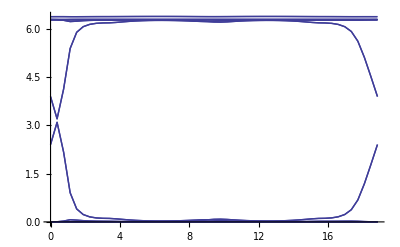

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<4Pi},{FCOR[-Pi,5Pi-T],T≥4Pi&&T≤5Pi},{FCOR[-6Pi+T,0],T≥5Pi&&T≤6Pi}}],{T,0,6Pi,6Pi/50},Filling->None,Evaluate[Joined->True]]
```

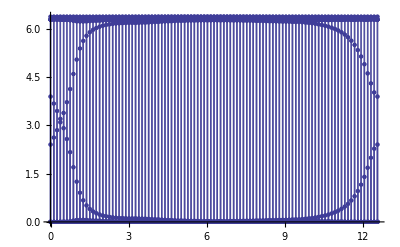

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{FCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,0,4Pi,4Pi/100},FillingStyle->None]
```

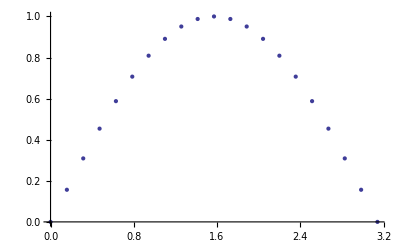

```mathematica
DiscretePlot[Sin[x],{x,0,Pi,Pi/20},Filling->None]
```

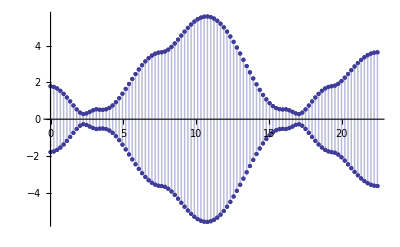

```mathematica
DiscretePlot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi,(4+Sqrt[2]+Sqrt[3])Pi/100},FillingStyle->None]
```